```mathematica
SetDirectory["/Users/paul/univ/eratosthenes/results/formatted/"]
benchLaptopPut = Import["out-GET2proc.264466"];
```

/Users/paul/univ/eratosthenes/results/formatted

```mathematica
fit = Fit[benchLaptopPut, {1,x},{x}]
fitPlot=Plot[fit,{x,0,250}];
```

2548.92+87.3835 x

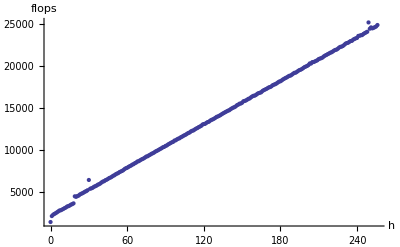

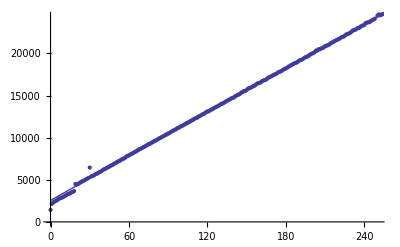

/Users/paul/univ/eratosthenes/report/img

bench-huy-get-p2.pdf

```mathematica
benchlaptopput=ListPlot[benchLaptopPut, AxesLabel->{"h", "flops"}]
both=Show[{fitPlot, benchlaptopput}]
SetDirectory["/Users/paul/univ/eratosthenes/report/img/"]
Export["bench-huy-get-p2.pdf", both]
```